# Advanced Scalable Multi-Beam Focusing for Indoor Optical Wireless Networks with IR Radiative Clusters Supplementary Material: Numerical Simulations

## Abstract :

Optical wireless networks emerge as a promising solution to the ever-growing data demand for user-centric indoor applications. This work demonstrates a novel approach to advance multi-user radiation patterns in indoor optical wireless networks by utilizing a cluster-based optical aperture comprising IR radiative elements. Spatially distributed IR clusters permit a non-uniform spherical wave model to focus the radiation in the near-field regime. By executing sub-clusters within main clusters and assigning them to groups for phase delay compensation, we ensure the generation of independent narrow beams focused on each receiver simultaneously. To mitigate the grating lobe formation, we incorporate a dual-carrier framework that introduces an effective wavelength for the system. Based on this theoretical model, we examine multi-beam focusing with a systematic arrangement of clusters on a planar ceiling. It follows a phased array within a phased array structure and incorporates a sub-cluster segmentation algorithm. We suggest optimizing cluster excitation based on receiver positions to enhance power efficiency and safety. This involves selecting the optimal clusters from a uniform array by solving a multiobjective non-convex binary optimization problem, aiming to maximize receiver intensity, minimize intensity variations, and reduce side lobes level. Instead of stochastic algorithms, we adopt a sparse relaxation-based weighted sum method that convexifies the binary space with L1 norm regularization compensating for convexity. The Transformed problem is solved deterministically via Nelder-Mead simplex without gradients. Simulated results confirm a better multi-beam focusing pattern, effectively balancing three objectives. Our findings pave the way for sustainable indoor optical wireless networks in next-generation communication.

Copyright © 2026 Sharadhi Gunathilake 
This code accompanies the publication: "Advanced Scalable Multi-Beam Focusing for Indoor Optical Wireless Networks with IR Radiative Clusters", provided for academic and research reference purposes only.

## Initialization and styling

```mathematica
ClearAll["Global`*"](*Clear Variables and memory*)
```

Define Colors :

```mathematica
c0=RGBColor[10/255,50/255,100/255];   (*Very Dark Blue*)
c1=RGBColor[12/255,54/255,105/255];
c2=RGBColor[14/255,58/255,110/255];
c3=RGBColor[16/255,62/255,115/255];
c4=RGBColor[18/255,66/255,120/255];
c5=RGBColor[20/255,70/255,130/255];   (*Dark Blue*)
c6=RGBColor[22/255,74/255,135/255];
c7=RGBColor[24/255,78/255,140/255];
c8=RGBColor[26/255,82/255,145/255];
c9=RGBColor[28/255,86/255,150/255];
c10=RGBColor[30/255,90/255,160/255];  (*Medium-Dark Blue*)
c11=RGBColor[34/255,98/255,165/255];
c12=RGBColor[38/255,106/255,170/255];
c13=RGBColor[42/255,114/255,175/255];
c14=RGBColor[46/255,118/255,180/255];
c15=RGBColor[52/255,124/255,184/255];  (*Medium Blue*)
c16=RGBColor[56/255,132/255,188/255];
c17=RGBColor[60/255,140/255,192/255];
c18=RGBColor[64/255,148/255,196/255];
c19=RGBColor[68/255,152/255,200/255];
c20=RGBColor[90/255,160/255,210/255];  (*Light-Medium Blue*)
c21=RGBColor[100/255,170/255,215/255];
c22=RGBColor[110/255,180/255,220/255];
c23=RGBColor[120/255,185/255,225/255];
c24=RGBColor[130/255,190/255,230/255]; (*Light Blue*)
c25=RGBColor[140/255,195/255,233/255];
c26=RGBColor[150/255,200/255,235/255];
c27=RGBColor[160/255,205/255,238/255];
c28=RGBColor[170/255,215/255,245/255]; (*Very Light Blue*)
c29=RGBColor[185/255,190/255,220/255];
c30=RGBColor[200/255,160/255,195/255];
c31=RGBColor[210/255,150/255,185/255];
c32=RGBColor[225/255,160/255,195/255];
c33=RGBColor[230/255,165/255,185/255];
c34=RGBColor[235/255,175/255,175/255]; (*Light Red-Purple*)
c35=RGBColor[240/255,150/255,160/255];
c36=RGBColor[245/255,130/255,150/255];
c37=RGBColor[245/255,130/255,140/255];
c38=RGBColor[245/255,130/255,130/255];
c39=RGBColor[245/255,130/255,120/255]; (*Light Red*)
c40=RGBColor[235/255,120/255,110/255];
c41=RGBColor[230/255,110/255,100/255];
c42=RGBColor[225/255,105/255,95/255];
c43=RGBColor[220/255,100/255,90/255];  (*Medium Red*)
c44=RGBColor[210/255,90/255,80/255];
c45=RGBColor[200/255,80/255,70/255];
c46=RGBColor[190/255,70/255,60/255];   (*Dark Red*)
c47=RGBColor[170/255,60/255,50/255];
c48=RGBColor[150/255,50/255,40/255];
c49=RGBColor[130/255,40/255,30/255];
c50=RGBColor[100/255,30/255,20/255];
```

## Numerical Simulations

### Defining functional and dimensional parameters

Functional parameters for the dual carrier framework

```mathematica
λd = 1.56*10^-6; (*data wavelength*)
wavelengthDiff =4*1.2*10^-12; 
λb = λd - wavelengthDiff; (*baseline wavelength*)
λe =2*(λd*λb)/(λd - λb);(*effective wavelength*)
```

Dimensional parameters of an indoor room

```mathematica
xLength=3;
yLength=4;
zHeight=3;
xMiddle=Round[xLength]/2;
yMiddle=Round[yLength]/2;
```

Dimensional parameters of optical cluster aperture of IR radiative elements

```mathematica
mx1=6; (*Cluster count along x axis*)
my1=8;(* Cluster count along y axis*)
nx1=6;(*IR elements in a cluster along x axis*)
ny1=6;(*IR elements in a cluster along y axis*)
```

```mathematica
Dis1=0.5;(* Distance between IR clusters is 0.5 m*)
dis1=λd/2;(* Distnace between nano radiating elements is half of the IR wavelength*)
```

### Multi-Beam focusing pattern of the proposed planar optical aperture

Define the sub-cluster segmentation algorithm

```mathematica
selectValidSubMatrixDimension[matrixRowCount_,matrixColCount_,subMatrixCount_]:=Module[{totalElems,subMatrixSize,possibleRowDimensions,r,c,validDimensions,mostSquareDimension},
totalElems=matrixRowCount*matrixColCount;
subMatrixSize=totalElems/subMatrixCount;
(*Find possible Row dimensions for the calculated submaitrxSize*)
possibleRowDimensions=Select[Divisors[subMatrixSize],Divisible[matrixRowCount,#]&];
(*find matching Column Size for the Possible Row Dimensions and then select possible couples which can accomadate subMatrix by finindg correct column sizes*)
validDimensions=Select[Table[{r,c=subMatrixSize/r},{r,possibleRowDimensions}],Divisible[matrixColCount,#[[2]]]&];
(*Select MSot squarer pairs and if there are tow select low row count with high col count*)
mostSquareDimension=MinimalBy[validDimensions,Abs[#[[1]]-#[[2]]]&];
(*If[Length[mostSquareDimension]>=1, Return[mostSquareDimension[[1]]],Return[mostSquareDimension]]*);
Return[mostSquareDimension[[1]]];
]
```

```mathematica
subdividingMatrix[uElems_,vElems_,userCount_]:=Module[{factors,nearestFactor,subMatrixDimension,matrix,r,c,u,v,m,n},
factors=Divisors[uElems*vElems];
(*Finding nearest factor for the given number of users*)
nearestFactor=SelectFirst[factors,#>=userCount&];
(*Find the best submatrix dimension for the given number of users*)
subMatrixDimension=selectValidSubMatrixDimension[uElems,vElems,nearestFactor];
subMatrixDimension
]
```

Define the multi-beam focusing pattern with dual carrier framework

```mathematica
beamFocusingPatternPlanar[λd_ ,λe_,x_,y_,z_,Dis_,dis_,mxClus_,myClus_,nxElems_,nyElems_,xMid_,yMid_,focalPoints_]:=Module[{arbitraryPoint,elementPoint,nx,ny,mx,my,clusterMidPoint,rt,rp,focalPointCount,subMatrixDim,r,c,m,n,assignedSubMatrices,beamFocusingPlanarCluster,rpI,deltaArrI},
arbitraryPoint={x,y,z};
elementPoint={xMid+(dis/2*(2*nx-nxElems-1)+Dis/2*(2*mx-mxClus-1)),yMid+(dis/2*(2*ny-nyElems-1)+Dis/2*(2*my-myClus-1)),zHeight};
clusterMidPoint={xMid+Dis/2*(2*mx-mxClus-1),yMid+Dis/2*(2*my-myClus-1),zHeight};
rt=EuclideanDistance[arbitraryPoint,clusterMidPoint];
rp=EuclideanDistance[arbitraryPoint,elementPoint];
focalPointCount=Length[focalPoints];
subMatrixDim=subdividingMatrix[nxElems,nyElems,focalPointCount];
r=subMatrixDim[[1]];
c=subMatrixDim[[2]];
assignedSubMatrices=1;
beamFocusingPlanarCluster=0;
For[m=1,m<=nxElems,m+=r,{
For[n=1,n<=nyElems,n+=c,{
If[assignedSubMatrices>focalPointCount,Break[],];
rpI=EuclideanDistance[focalPoints[[assignedSubMatrices]],elementPoint];
deltaArrI=rp-rpI;
beamFocusingPlanarCluster+=∑_(nx=m)^(m+r-1) ∑_(ny=n)^(n+c-1) (Cos[(2π)/λe*deltaArrI]*Exp[-ⅈ*(2π)/λd*deltaArrI])/rt;
assignedSubMatrices++;
}]
}];
Table[beamFocusingPlanarCluster,{mx,1,mxClus},{my,1,myClus}]
]
```

#### Normalized intensity pattern for 2 receivers : Figure 05

Plotting the normalized beam intensity patterns

```mathematica
maxRadiationY[ymin_,ymax_,yres_,radiation_]:=Module[{tempy},
tempy=Table[{Abs[radiation]},{y,ymin,ymax,yres}];
Max[tempy]
]
```

```mathematica
myColorFunction=Function[{z},Which[z<=-25,c0,z<=-24.5,c1,z<=-24,c2,z<=-23.5,c3,z<=-23,c4,z<=-22.5,c5,z<=-22,c6,z<=-21.5,c7,z<=-21,c8,z<=-20.5,c9,z<=-20,c10,z<=-19.5,c11,z<=-19,c12,z<=-18.5,c13,z<=-18,c14,z<=-17.5,c15,z<=-17,c16,z<=-16.5,c17,z<=-16,c18,z<=-15.5,c19,z<=-15,c20,z<=-14.5,c21,z<=-14,c22,z<=-13.5,c23,z<=-13,c24,z<=-12.5,c25,z<=-12,c26,z<=-11.5,c27,z<=-11,c28,z<=-10.5,c29,z<=-10,c30,z<=-9.5,c31,z<=-9,c32,z<=-8.5,c33,z<=-8,c34,z<=-7.5,c35,z<=-7,c36,z<=-6.5,c37,z<=-6,c38,z<=-5.5,c39,z<=-5,c40,z<=-4.5,c41,z<=-4,c42,z<=-3.5,c43,z<=-3,c44,z<=-2.5,c45,z<=-2,c46,z<=-1.5,c47,z<=-1,c48,z<=-0.5,c49,True,c50]];
```

```mathematica
plotPlanarRadiationXY[data_,fontSize_]:=Module[{normalizedPlot},
normalizedPlot=ListContourPlot[data,ContourStyle->None,Contours->50,ColorFunction->myColorFunction,ColorFunctionScaling->False,FrameLabel->{{"x axis (m)",None},{"y axis (m)",None}},LabelStyle->Directive[Black,fontSize,FontFamily->"Times"],PlotLegends->BarLegend[{Automatic,{-25,1}},50,LegendMarkerSize->{Automatic,360},LabelStyle->Directive[Black,fontSize,FontFamily->"Times"]],PlotLabel->Style["Normalized Intensity dB ",fontSize,Black,FontFamily->"Times"],PlotRange->All,ImageSize->{360,400}]
]

zoomplotPlanarRadiationXY[data_]:=Module[{normalizedPlot},
normalizedPlot=ListContourPlot[data,ContourStyle->None,Contours->50,ColorFunction->myColorFunction,ColorFunctionScaling->False,LabelStyle->Directive[Black,14,FontFamily->"Times"],PlotRange->All,ImageSize->{200,220}]
]
```

Define receiver positions in the room

```mathematica
userLocations1={{1.6,2.3,0.75},{2.5,0.8,0.75}};(*for receiver Subscript[R, 1] and receiver Subscript[R, 2] repectively*)
```

Generating normalized intensity pattern for 2 users

```mathematica
radiationXY1=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations1],2]];
datapair1=ParallelTable[radiationXY1,{x,0,xLength,0.1},{y,0,yLength,0.1}];
dataPair1Max=Max[datapair1];
```

```mathematica
plotDataPair1=Flatten[ParallelTable[{y,x,20*Log[10,radiationXY1/dataPair1Max]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
normalizedPlot1=plotPlanarRadiationXY[plotDataPair1,15];
```

```mathematica
plotAnnotations1=Graphics[{EdgeForm[{Dashed,RGBColor[0.6,0.6,0.6]}],(*Outline style for the rectangle*)FaceForm[None],Rectangle[{userLocations1[[1,2]]-0.25,userLocations1[[1,1]]-0.25},{userLocations1[[1,2]]+0.25,userLocations1[[1,1]]+0.25}],Rectangle[{userLocations1[[2,2]]-0.25,userLocations1[[2,1]]-0.25},{userLocations1[[2,2]]+0.25,userLocations1[[2,1]]+0.25}]}];
```

Normalized intensity main plot

```mathematica
mainPlotWithAnnotations=Show[normalizedPlot1,plotAnnotations1]
```

-Graphics-

Normalized intensity Zoomed plot at receiver 1

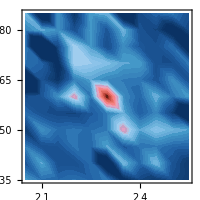

```mathematica
zoomDataPair1=Flatten[ParallelTable[{y,x,20*Log[10,radiationXY1/dataPair1Max]},{y,userLocations1[[1,2]]-0.25,userLocations1[[1,2]]+0.25,0.05},{x,userLocations1[[1,1]]-0.25,userLocations1[[1,1]]+0.25,0.05}],1];
zoomplot1=zoomplotPlanarRadiationXY[zoomDataPair1]
```

Normalized intensity Zoomed plot at receiver 2

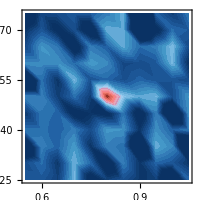

```mathematica
zoomDataPair2=Flatten[ParallelTable[{y,x,20*Log[10,radiationXY1/dataPair1Max]},{y,userLocations1[[2,2]]-0.25,userLocations1[[2,2]]+0.25,0.05},{x,userLocations1[[2,1]]-0.25,userLocations1[[2,1]]+0.25,0.05}],1];
zoomplot2=zoomplotPlanarRadiationXY[zoomDataPair2]
```

#### Normalized beam focusing pattern for 2 receivers: figure 06

Plotting the normalized beam focusing  patterns

```mathematica
plotRadiationY[dataPair_,yMin_,yMax_,axisLabel_,location_,user_]:=Module[{labelSpot,specialTick,normalizedPlot},
If[axisLabel=="y-axis (m)",{specialTick=location[[2]],
If[location[[2]]>=2.5,labelSpot={0.7,0.9},labelSpot={3.3,0.9}]}
,{specialTick=location[[1]],If[location[[1]]>=2.5,labelSpot={0.7,0.9},labelSpot={2.5,0.9}]}];
normalizedPlot=ListLinePlot[dataPair,PlotRange->{{yMin,yMax},{0,1}},AxesOrigin->{0,0},Frame->{{True,False},{True,False}},PlotStyle->Directive[Thickness[0.006],RGBColor[0,0.5,0.5]],LabelStyle->Directive[Black,12,FontFamily->"Times New Roman"],FrameLabel->{axisLabel,"ψ (r)"},Epilog->{Text[Style[Row[{Subscript["R",user],": ("<>StringJoin[Riffle[ToString/@location,", "]]<>")"}],FontFamily->"Times New Roman",FontSize->12],labelSpot]},FrameTicks->{Join[Table[If[Mod[i,1]==0,{i,ToString[i]<>".0"},{i,i}],{i,yMin,yMax,1}],{{specialTick,Style[ToString[specialTick],FontFamily->"Times New Roman",FontSize->12,RGBColor[1,0.5,0.5]]}}],Automatic},ImageSize->{400,250},AspectRatio->Full,GridLines->{{},{{1,Dashed}}},GridLinesStyle->Directive[Darker[Gray],Dashed]]
]
```

```mathematica
radiationAlongX[user_,userLocations_,max_]:=Module[{radiationWithX,radiationWithXtr,dataPoints,dataValues,dataValuesMax,dataPair},
radiationWithX=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,userLocations[[user,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations],2]];
radiationWithXtr=radiationWithX/.x->y;
dataPoints=Table[y,{y,0,xLength,0.001}];
dataValues=Table[radiationWithXtr,{y,0,xLength,0.001}];
dataValuesMax=Max[dataValues];
dataPair=Transpose[{dataPoints,dataValues/max}];
Print[plotRadiationY[dataPair,0,xLength,"x-axis (m)",userLocations[[user]],user]]
]
```

```mathematica
radiationAlongY[user_,userLocations_,max_]:=Module[{radiationWithY,dataPoints,dataValues,dataValuesMax,dataPair},
radiationWithY=Abs[Total[beamFocusingPatternPlanar[λd,λe,userLocations[[user,1]],y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations],2]];
dataPoints=Table[y,{y,0,yLength,0.001}];
dataValues=Table[radiationWithY,{y,0,yLength,0.001}];
dataValuesMax=Max[dataValues];
dataPair=Transpose[{dataPoints,dataValues/max}];
Print[plotRadiationY[dataPair,0,yLength,"y-axis (m)",userLocations[[user]],user]]
]
```

Subfigure a: Normalized beam focusing pattern along x-axis at y = 2.3

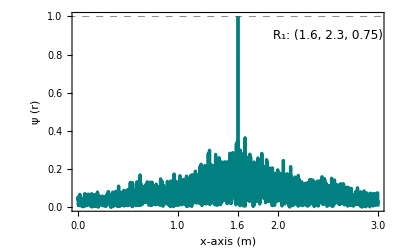

```mathematica
crosSecPlot1=radiationAlongX[1,userLocations1,dataPair1Max]
```

Subfigure b: Normalized beam focusing pattern along y-axis at  x = 1.6

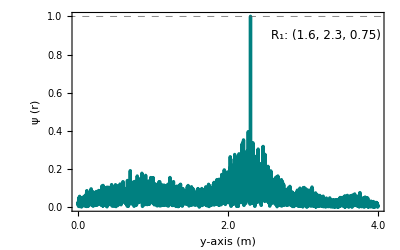

```mathematica
crosSecPlot2=radiationAlongY[1,userLocations1,dataPair1Max]
```

Subfigure c: Normalized beam focusing pattern along x-axis at  y = 0.8

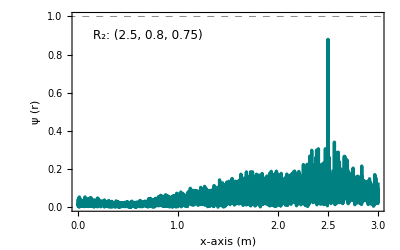

```mathematica
crosSecPlot3=radiationAlongX[2,userLocations1,dataPair1Max]
```

Subfigure d: Normalized beam focusing pattern along y-axis at  x = 2.5

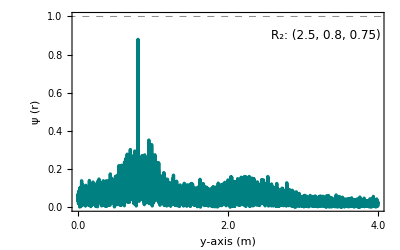

```mathematica
crosSecPlot4=radiationAlongY[2,userLocations1,dataPair1Max]
```

#### Finding peak side lobe level (PSLL) for the given 2 receiver configuration

Defining PSLL

```mathematica
findPlanarSLL[focalPoints_,maxBeamVal_,clusterExcitationPattern_]:=Module[{locationList,i,radiationList,maxPair={},maxPairList={},maxSll,maxInt,psll,psllLocation},
For[i=1,i<=Length[focalPoints],i++,
locationList=DeleteCases[Flatten[Table[{x,y},{x,focalPoints[[i,1]]-0.5,focalPoints[[i,1]]+0.5,0.05},{y,focalPoints[[i,2]]-0.5,focalPoints[[i,2]]+0.5,0.05}],1],{x_,y_}/;((focalPoints[[i,1]]-0.005<=x<= focalPoints[[i,1]]+0.005) && (focalPoints[[i,2]]-0.005<=y<= focalPoints[[i,2]]+0.005))];
radiationList =ParallelTable[{Total[beamFocusingPatternPlanar[λd,λe,locationList[[j,1]],locationList[[j,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,focalPoints]*clusterExcitationPattern,2],{locationList[[j,1]],locationList[[j,2]]}},{j,1,Length[locationList]}]; 
maxPair=First@MaximalBy[radiationList,Abs[First[#]]&];
AppendTo[maxPairList,maxPair]
] ;
maxInt=Abs[maxBeamVal];
maxSll=First@MaximalBy[maxPairList,Abs[First[#]]&];
psll=20*Log10[Abs[maxSll[[1]]]/maxInt];
psllLocation={maxSll[[2]][[1]],maxSll[[2]][[2]],0.75};
{psll,psllLocation}
];
```

Find PSLL for given R_1 and R_2 receivers

```mathematica
fullExcitationPattern=fullExcitationPattern=ConstantArray[1,{mx1,my1}];
psllResult1=findPlanarSLL[userLocations1,dataPair1Max,fullExcitationPattern];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[psllResult1[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[#,0.01]&/@psllResult1[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -9.12 dB
PSLL Location : | {1.5,2.35,0.75}

#### Evaluating Max-Min Power Ratio (MMPR) in a Two-Receiver System Under Varying Detector Area.

```mathematica
beamPower[config_,userlocation_,detectorArea_]:=Module[{x0,x1,y0,y1,beamPower,η=377,α=1},
x0=userlocation[[1]]-detectorArea/2;
x1=userlocation[[1]]+detectorArea/2;
y0=userlocation[[2]]-detectorArea/2;
y1=userlocation[[2]]+detectorArea/2;
beamPower=α/(2*η)*Quiet[NIntegrate[(config)^2,{x,x0,x1},{y,y0,y1}]]
];
```

```mathematica
beamPowerForUsers[config_,userLocations_,detectorArea_]:=Module[{beamPrList={},j,beamPr},
For[j=1,j<=Length[userLocations],j++,
beamPr=beamPower[config,userLocations[[j]],detectorArea];
AppendTo[beamPrList,beamPr];
];
beamPrList
];
```

```mathematica
mmprCal[radiationXY_,userLocations_]:=Module[{relativePowerList={},i,beamPrList={}},
For[i=1,i<=10,i++,
beamPrList=beamPowerForUsers[radiationXY,userLocations,i*10^-3];
AppendTo[relativePowerList,Min[beamPrList]/Max[beamPrList]];
];
relativePowerList
];
```

Finding MMPR for R_1 and R_2 receivers while changing the detector area:Figure 07

```mathematica
userPowerList1=mmprCal[radiationXY1,userLocations1];
detectorAreaList={1,4,9,16,25,36,49,64,81,100};
```

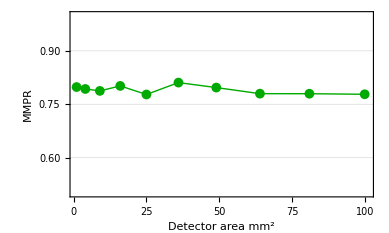

```mathematica
ListLinePlot[Transpose[{detectorAreaList,userPowerList1}],PlotMarkers->{"●",10},(*Adds dots at the points*)PlotStyle->Directive[Darker[Green],Thick],Frame->True,FrameStyle->{Black,None,Black,None},FrameLabel->{Style["Detector area mm^2",FontFamily->"Times",FontSize->14,Black],Style[" MMPR ",FontFamily->"Times",FontSize->14,Black]},FrameTicksStyle->Directive[Black,FontSize->12,FontFamily->"Times New Roman"],GridLines->{None,Automatic},GridLinesStyle->Directive[Dashed,Gray],PlotRange->{{0.75,101},{0.5,1}},AspectRatio->0.6,ImagePadding->{{40,20},{40,20}} (*Prevents clipping*)]
```

```mathematica
Mean[userPowerList1]*100
```

79.0292

### Find selective Cluster Excitation pattern using sparse relaxation-based weighted sum algorithm

#### Defining the sparse relaxation based MOO algorithm (SR)

consider same receiver locations of R_1 and R_2 inside the same indoor room setup.

```mathematica
userLocations2={{1.6,2.3,0.75},{2.5,0.8,0.75}};
```

Define the algorithm parameters

```mathematica
maxIterations=5;(* iteration count for algorithm execution *)
```

Define sparse relaxation-based weighted sum algorithm with L_1 norm regularization.

```mathematica
clusterThinningAlgo[userLocations_,onCount_,weightCom_]:=Module[{radiationAtUseri={},i,j,modRadiationListForUsers={},weights,vars,val=0,valSet={},xyList={},objectiveFunction=0,radiationData ,sllDataSet={},sllData=0,thresholdIntensityL,thresholdIntensityU,mMin=6,mMax=40,constraints,solution,extractedSolution,previousSolution,sortedSolution,finalSolution,optVal, optValSet={},optSllData},

weights=ConstantArray[1,mx1*my1];(*Initialize the weight matrix with all values set to 1 *)
vars=Array[b,mx1*my1];(*Initialize the matrix H with unknowns *)

(*Find intensities at user locations*)
For[i=1,i<=Length[userLocations],i++,
radiationAtUseri=beamFocusingPatternPlanar[λd,λe,userLocations[[i,1]],userLocations[[i,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations];
AppendTo[modRadiationListForUsers,Flatten[radiationAtUseri,1]];
];
For[i=1,i<=Length[userLocations],i++,
{val=Abs[modRadiationListForUsers[[i]].vars]^2,
AppendTo[valSet,val]}
];

(*Find PSLL*)
For[i=1,i<=Length[userLocations],i++,
xyList=DeleteCases[Flatten[Table[{x,y},{x,userLocations[[i,1]]-0.5,userLocations[[i,1]]+0.5,0.1},{y,userLocations[[i,2]]-0.5,userLocations[[i,2]]+0.5,0.1}],1],{x_,y_}/;((userLocations[[i,1]]-0.005<=x<= userLocations[[i,1]]+0.005) && (userLocations[[i,2]]-0.005<=y<= userLocations[[i,2]]+0.005))];
radiationData =ParallelTable[Flatten[beamFocusingPatternPlanar[λd,λe,xyList[[j,1]],xyList[[j,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations],1],{j,1,Length[xyList]}]; 
sllData=Max[Abs[radiationData.vars]^2];
AppendTo[sllDataSet,sllData];
] ;

(*objective statement with Subscript[L, 1] norm regularization. Considered the weighted sum of three objectives: maximizing intensity at receiver locations, minimizing intensity variation, minimizing peak side lobe level*)
objectiveFunction=weightCom[[1]]*Mean[valSet]-weightCom[[2]]*StandardDeviation[valSet]-weightCom[[3]]*Max[sllDataSet]-1/onCount*(weights.vars);
thresholdIntensityL=0.9*1/Length[userLocations]*((mMin*nx1*ny1)/EuclideanDistance[{xMiddle,yMiddle,zHeight},{xLength,yLength,0}])^2;(*Lower intensity threshold*)
thresholdIntensityU=1.1*1/Length[userLocations]*((mMax*nx1*ny1)/EuclideanDistance[{xMiddle,yMiddle,zHeight},{xMiddle,yMiddle,0}])^2;(*Upper intensity threshold*)

constraints={0<=vars<=1,Total[vars]==onCount,Table[thresholdIntensityL<=valSet[[i]]<=thresholdIntensityU,{i,1,Length[userLocations]}]};(*Constraints to consider*)

extractedSolution=Array[0,mx1*my1];
previousSolution=Array[0,mx1*my1];
(*Perform Nelder-Mead simplex method on the transformed objective statment in iterative manner*)
For[i=1,i<=maxIterations,i++,
previousSolution=extractedSolution;
solution=NMaximize[{objectiveFunction,constraints},vars,Method->"NelderMead"];
(*Extract the solution : Numerical solutions for variables*)
extractedSolution=Values[solution[[2]]]; 

(*Update weights for the next iteration*)
weights=1-extractedSolution/Max[extractedSolution];

(*Check for convergence*)
If[Norm[extractedSolution-previousSolution,Infinity]<10^-3,Break[],]; 
];

(*Controlled rounding to enforce binary solution*);
sortedSolution=Sort[Thread[{extractedSolution,Range[mx1*my1]}],#1[[1]]>#2[[1]]&];
finalSolution=ConstantArray[0,mx1*my1]; (*Initialize all to 0 (inactive)*)
Do[finalSolution[[sortedSolution[[i,2]]]]=1,{i,1,onCount} ];(*Select top onCluster indices to be active (set to 1)*)

(*Check the objectives space for the finalized binary solution *)
For[i=1,i<=Length[userLocations],i++,
{optVal=Abs[modRadiationListForUsers[[i]].finalSolution]^2,
AppendTo[optValSet,optVal]}
];
optSllData=Max[Abs[radiationData.finalSolution]^2];

(*Return the solution*)
 {ArrayReshape[finalSolution,{mx1,my1}],Mean[optValSet],StandardDeviation[optValSet],optSllData}
]
```

#### Evaluating the Pareto Optimal behaviour for 3 objectives on different weight combinations

This for loop generates the objective space for 60 different weight combinations when only 18 IR radiative clusters are active. In each iteration, it computes the selective excitation pattern using the sparse-relaxation based weighted sum algorithm defined above. As a result, completing the loop will take a considerable amount of time.

```mathematica
onClusters=18;(*On cluster count*)
nCount=10;dataList={};
```

```mathematica
For[i=0,i<=nCount,i++ ,
For[j=0,j<=(nCount-i),j++,
{
k=nCount-i-j;
result={};
weightCombination={i/nCount,j/nCount,k/nCount};
result=clusterThinningAlgo[userLocations2,onClusters,weightCombination];
AppendTo[dataList,{weightCombination,result[[2]],result[[3]],result[[4]]}];
}
]
];
```

```mathematica
normalizedObjective1=dataList[[All,2]]/Max[dataList[[All,2]]];
normalizedObjective2=dataList[[All,3]]/Max[dataList[[All,3]]];
normalizedObjective3=dataList[[All,4]]/Max[dataList[[All,4]]];
weightList=dataList[[All,1]];
```

```mathematica
combinedNormalizedObjectiveList=Transpose[{normalizedObjective1,normalizedObjective2,normalizedObjective3}];
specialPoint={0.9120292104894643,0.07734797110971665,0.35232309303418474};
posDatPoint=Position[combinedNormalizedObjectiveList,specialPoint];
```

```mathematica
selectedWeightCombination=Flatten[weightList[[posDatPoint[[1]]]],1](* Selected weight combination for subsequent evaluations*)
```

{1/5,1/5,3/5}

```mathematica
newCombinedNormalizedObjectiveList=DeleteCases[combinedNormalizedObjectiveList,specialPoint];
```

Objective space for all different weight combinations: Figure 08

```mathematica
plot3D=ListPointPlot3D[{newCombinedNormalizedObjectiveList,{specialPoint}},AxesLabel->{"I_μ(H, r_q)","","S(H,q)"},PlotStyle->{Directive[{Blue,PointSize[0.02]}],Directive[{Darker[Red],PointSize[0.02]}]},LabelStyle->Directive[Black,12,FontFamily->"Times New Roman"],Boxed->False,Axes->True,Method->{"AxesDuringInteraction","Locked"},ViewPoint->{1.5,3.4,0.6},Ticks->{Table[i,{i,0,1,0.2}],Table[i,{i,0,1,0.2}],Table[i,{i,0,1,0.2}]},PlotLabel->" Normalized objective space", AspectRatio->1,FaceGrids->{{-1,0,0},{0,-1,0},{0,0,-1}},PlotRange->{{0,1},{0,1},{0,1}}];
plotLabel=Graphics3D[Text[Style[ToString[Round[specialPoint,0.01]],FontSize->12,FontFamily->"Times New Roman",FontColor->Darker[Red]],specialPoint+{-0.1,0.02,-0.35}]];
```

```mathematica
plotLabel2=Graphics3D[{Darker[Red],Arrowheads[0.05],Thickness[Tiny],Arrow[{specialPoint+{-0.03,0.02,-0.30},specialPoint}]}];
```

```mathematica
customLabel=Graphics3D[{Text[Style["I_σ(H, r_q)",FontSize->12,FontColor->Black,FontFamily->"Times New Roman"],{0.2,0.5,1}]}];
```

```mathematica
Show[plot3D,plotLabel,plotLabel2,customLabel]
```

-Graphics3D-

#### Find the selective cluster excitation pattern and evaluate their resulting beam focusing pattern for varying active cluster counts: figure 09 and table 2

```mathematica
weightCombination1={0.2,0.2,0.6};(*Selected weight combination from early section*)
```

For same R1 and R2 receivers locations, This loop generates cluster excitation pattern and corresponding PSLL and MMPR for varying cluster activation count from 6 to 40. As a result, completing the loop will take a considerable amount of time.

```mathematica
clusterExcitationPatternGen[mMin_,mMax_,userLocation_,weightCom_]:=Module[{i,results={},clusterExcitationPatterncX,thinnedClusterRadiationXY,datapairMax,lsllResult={},userPowerList={}},
For[i=mMin,i<=mMax,i++,
clusterExcitationPatterncX=clusterThinningAlgo[userLocation,i,weightCom][[1]];
thinnedClusterRadiationXY=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocation]*clusterExcitationPatterncX,2]];
datapairMax=Max[ParallelTable[thinnedClusterRadiationXY,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
lsllResult=findPlanarSLL[userLocation,datapairMax,clusterExcitationPatterncX];
userPowerList=beamPowerForUsers[thinnedClusterRadiationXY,userLocation,10*10^-3];
AppendTo[results,{clusterExcitationPatterncX,lsllResult,userPowerList}];
];
results
];
```

```mathematica
excitationPatternList=clusterExcitationPatternGen[6,40,userLocations2,weightCombination1]
```

{{{{1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-3.30551,{2.35,0.7,0.75}},{0.0000338996,0.0000387067}},{{{1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-2.93926,{1.55,2.2,0.75}},{0.0000411586,0.0000440299}},{{{1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0},{0,1,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-3.66416,{2.65,1.,0.75}},{0.0000470443,0.0000505605}},{{{1,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-4.88066,{1.8,2.15,0.75}},{0.0000531497,0.0000562864}},{{{1,0,0,0,0,0,0,0},{0,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}},{-5.1719,{2.65,1.,0.75}},{0.0000626707,0.0000600218}},{{{1,0,0,1,0,0,0,0},{0,0,1,0,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,0,0,1,0,0,0,0}},{-5.12168,{1.4,2.3,0.75}},{0.0000648677,0.0000676235}},{{{1,0,0,1,0,0,0,0},{0,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0}},{-6.12424,{1.45,2.15,0.75}},{0.0000743125,0.0000723259}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,0,0,1,0,0,0,0}},{-6.13935,{2.2,0.55,0.75}},{0.0000788601,0.0000762154}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,0,0,1,0,0,0,0}},{-5.88161,{2.5,0.85,0.75}},{0.000082714,0.0000847291}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,0,1,1,0,0,0,0}},{-5.5013,{2.5,0.85,0.75}},{0.0000898321,0.0000913597}},{{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0},{0,1,1,1,0,0,0,0}},{-6.58343,{2.35,1.1,0.75}},{0.0000967748,0.0000947916}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,1,1,0,0,0},{0,1,1,1,0,0,0,0}},{-5.57683,{2.5,0.85,0.75}},{0.000101893,0.00010709}},{{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{1,1,0,1,1,0,0,0},{0,1,1,1,0,0,0,0}},{-7.11461,{1.8,2.15,0.75}},{0.000108014,0.000112174}},{{{1,0,0,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,1,0,0,0,0},{1,1,0,0,1,0,0,0},{1,1,1,1,0,0,0,0}},{-7.47999,{1.65,2.25,0.75}},{0.000110964,0.000117939}},{{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,0,0,0,0}},{-8.32051,{1.65,2.25,0.75}},{0.000116339,0.00012258}},{{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,0,0,0,0,0},{1,1,0,0,1,0,0,0},{1,1,1,1,1,0,0,0}},{-8.72623,{2.65,0.6,0.75}},{0.000123755,0.000124247}},{{{1,0,1,1,0,0,0,0},{1,0,1,0,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,0,0,0}},{-7.72268,{2.5,0.85,0.75}},{0.000128443,0.000133745}},{{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,0,1,0,0,0},{1,1,1,1,1,0,0,0}},{-7.62253,{1.8,2.25,0.75}},{0.000137696,0.000133062}},{{{1,1,1,1,0,0,0,0},{1,0,1,0,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,1,1,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,0,0,0}},{-7.42246,{2.5,0.85,0.75}},{0.000143718,0.000144273}},{{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,0,0}},{-8.76218,{1.4,2.35,0.75}},{0.000151585,0.000146082}},{{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,1,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,0,0}},{-8.34427,{1.4,2.35,0.75}},{0.000159378,0.000148818}},{{{1,1,1,1,0,0,0,0},{1,0,1,0,0,1,1,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.42521,{2.5,0.85,0.75}},{0.000162907,0.000153938}},{{{1,1,1,1,0,0,0,0},{1,0,1,0,0,1,1,0},{1,1,1,0,0,1,0,0},{1,0,1,1,1,1,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.03699,{1.4,2.35,0.75}},{0.000171904,0.000158278}},{{{1,1,1,1,0,1,0,0},{1,0,1,0,0,1,0,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.67832,{1.4,2.35,0.75}},{0.000173315,0.000159453}},{{{1,1,1,1,0,1,0,0},{1,0,1,0,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.34677,{1.4,2.35,0.75}},{0.000179894,0.000163701}},{{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-7.67224,{1.4,2.35,0.75}},{0.000187574,0.000169568}},{{{1,1,1,1,0,1,0,0},{1,0,1,1,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,0}},{-8.3721,{1.4,2.35,0.75}},{0.000194873,0.000177189}},{{{1,1,1,1,0,1,0,0},{1,1,1,0,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-8.59366,{1.4,2.35,0.75}},{0.000196998,0.000179771}},{{{1,1,1,1,0,1,0,0},{1,1,1,1,0,1,1,0},{1,1,1,0,0,1,0,1},{1,0,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-8.17743,{1.4,2.35,0.75}},{0.000210875,0.000181291}},{{{1,1,1,1,0,1,0,0},{1,1,1,1,0,1,1,0},{1,1,1,0,0,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-8.39417,{1.4,2.35,0.75}},{0.000217172,0.000189127}},{{{1,1,1,1,0,1,0,0},{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-9.17574,{1.4,2.35,0.75}},{0.000215634,0.000193384}},{{{1,1,1,1,0,1,0,0},{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,0,1},{1,1,1,1,1,1,1,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-9.09852,{1.75,2.2,0.75}},{0.000222319,0.000194532}},{{{1,1,1,1,0,1,1,0},{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,1}},{-8.67717,{1.4,2.35,0.75}},{0.000227616,0.000197581}},{{{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-9.09559,{1.4,2.35,0.75}},{0.000231977,0.0002002}},{{{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}},{-9.48056,{1.5,2.35,0.75}},{0.000238325,0.000204752}}}

SubFigure a : Algorithm results for active cluster count M’ = 40

```mathematica
clusterExcitationPatterncX1=excitationPatternList[[35,1]](*Select the excitation pattern for M'=35 from excitation pattern list*)
```

{{1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,1,1}}

```mathematica
thinnedClusterRadiationXY1=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations2]*clusterExcitationPatterncX1,2]];
thinnedDatapair1Max=Max[ParallelTable[thinnedClusterRadiationXY1,{x,0,xLength,0.1},{y,0,yLength,0.1}]]
```

271.69

```mathematica
thinnedPlotDataPair1=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiationXY1/thinnedDatapair1Max]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
```

```mathematica
plotPlanarRadiationXY[thinnedPlotDataPair1,21]
```

-Graphics-

Finding PSLL for the obtained excitation pattern

```mathematica
thinnedPsllResult1=excitationPatternList[[35,2]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[thinnedPsllResult1[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],thinnedPsllResult1[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -9.48 dB
PSLL Location : | {1.5,2.35,0.75}

Finding the MMPR for receivers

```mathematica
thinnedPowerList1=excitationPatternList[[35,3]];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[thinnedPowerList1]/Max[thinnedPowerList1],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.859

SubFigure b : Algorithm results for active cluster count M’ = 26

```mathematica
clusterExcitationPatterncX2=excitationPatternList[[21,1]]
```

{{1,1,1,1,0,0,0,0},{1,0,1,1,0,1,1,0},{1,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,0},{1,1,0,1,1,0,0,0},{1,1,1,1,1,1,0,0}}

```mathematica
thinnedClusterRadiationXY2=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations2]*clusterExcitationPatterncX2,2]];
thinnedDatapair2Max=Max[ParallelTable[thinnedClusterRadiationXY2,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair2=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiationXY2/thinnedDatapair2Max]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
```

```mathematica
plotPlanarRadiationXY[thinnedPlotDataPair2,21]
```

-Graphics-

Finding PSLL for the obtained excitation pattern

```mathematica
thinnedPsllResult2=excitationPatternList[[21,2]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[thinnedPsllResult2[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],thinnedPsllResult2[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -8.34 dB
PSLL Location : | {1.4,2.35,0.75}

Finding the MMPR for receivers

```mathematica
thinnedPowerList2=excitationPatternList[[21,3]];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[thinnedPowerList2]/Max[thinnedPowerList2],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.934

SubFigure c : Algorithm results for active cluster count M’ = 18

```mathematica
clusterExcitationPatterncX3=excitationPatternList[[13,1]]
```

{{1,0,1,1,0,0,0,0},{1,0,1,1,0,1,0,0},{0,1,1,0,0,0,0,0},{1,0,1,0,0,0,0,0},{1,1,0,1,1,0,0,0},{0,1,1,1,0,0,0,0}}

```mathematica
thinnedClusterRadiationXY3=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations2]*clusterExcitationPatterncX3,2]];
thinnedDatapair3Max=Max[ParallelTable[thinnedClusterRadiationXY3,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair3=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiationXY3/thinnedDatapair3Max]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
```

```mathematica
plotPlanarRadiationXY[thinnedPlotDataPair3,21]
```

-Graphics-

Finding PSLL for the obtained excitation pattern

```mathematica
thinnedPsllResult3=excitationPatternList[[13,2]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[thinnedPsllResult3[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],thinnedPsllResult3[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -7.11 dB
PSLL Location : | {1.8,2.15,0.75}

Finding the MMPR for receivers

```mathematica
thinnedPowerList3=excitationPatternList[[13,3]];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[thinnedPowerList3]/Max[thinnedPowerList3],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.963

SubFigure d: Algorithm results for active cluster count M’ = 6

```mathematica
clusterExcitationPatterncX4=excitationPatternList[[1,1]]
```

{{1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0}}

```mathematica
thinnedClusterRadiationXY4=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations2]*clusterExcitationPatterncX4,2]];
thinnedDatapair4Max=Max[ParallelTable[thinnedClusterRadiationXY4,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair4=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiationXY4/thinnedDatapair4Max]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
```

```mathematica
plotPlanarRadiationXY[thinnedPlotDataPair4,21]
```

-Graphics-

Finding PSLL for the obtained excitation pattern

```mathematica
thinnedPsllResult4=excitationPatternList[[1,2]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[thinnedPsllResult4[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],thinnedPsllResult4[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -3.31 dB
PSLL Location : | {2.35,0.7,0.75}

Finding the MMPR for receivers

```mathematica
thinnedPowerList4=excitationPatternList[[1,3]];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[thinnedPowerList4]/Max[thinnedPowerList4],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.876

#### Compare the sparse relaxation based algorithm with Simulated Annealing(SA) algorithm: figure10

Define SA algorithm with  weighted sum objective statement.

```mathematica
clusterThinningSAAlgo[userLocations_,onCount_,weightCom_]:=Module[{radiationListForUsers={},modRadiationListForUsers={},i,val,valSet={},xyList={},radiationData,sllDataSet={},sllData=0,objectiveFunction=0,binaryVars,initialGuess,thresholdIntensityL,thresholdIntensityU,mMin=6,mMax=40,constraints,solution},

For[i=1,i<=Length[userLocations],i++,
radiationListForUsers=beamFocusingPatternPlanar[λd,λe,userLocations[[i,1]],userLocations[[i,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations];
AppendTo[modRadiationListForUsers,Flatten[radiationListForUsers,1]];
];

binaryVars=Array[b,mx1*my1];
initialGuess=RandomInteger[{0,1},Length[binaryVars]];

For[i=1,i<=Length[userLocations],i++,
{val=(Abs[modRadiationListForUsers[[i]].binaryVars])^2,
AppendTo[valSet,val]}
];

For[i=1,i<=Length[userLocations],i++,
xyList=DeleteCases[Flatten[Table[{x,y},{x,userLocations[[i,1]]-0.5,userLocations[[i,1]]+0.5,0.05},{y,userLocations[[i,2]]-0.5,userLocations[[i,2]]+0.5,0.05}],1],{x_,y_}/;((userLocations[[i,1]]-0.005<=x<= userLocations[[i,1]]+0.005) && (userLocations[[i,2]]-0.005<=y<= userLocations[[i,2]]+0.005))];
radiationData =ParallelTable[Flatten[beamFocusingPatternPlanar[λd,λe,xyList[[j,1]],xyList[[j,2]],0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations],1],{j,1,Length[xyList]}]; 
sllData=Max[Abs[radiationData.binaryVars]];
AppendTo[sllDataSet,sllData];
] ;

objectiveFunction=weightCom[[1]]*Mean[valSet]-weightCom[[2]]*StandardDeviation[valSet]-weightCom[[3]]*Max[sllDataSet];(*Objective statement*)
thresholdIntensityL=0.9*1/Length[userLocations]*((mMin*nx1*ny1)/EuclideanDistance[{xMiddle,yMiddle,zHeight},{xLength,yLength,0}])^2;(*Lower intensity limit*)
thresholdIntensityU=1.1*1/Length[userLocations]*((mMax*nx1*ny1)/EuclideanDistance[{xMiddle,yMiddle,zHeight},{xMiddle,yMiddle,0}])^2;(*Upper intensity limit*)
constraints={0<=binaryVars<=1,binaryVars∈Integers,Total[binaryVars]==onCount,Table[thresholdIntensityL<=valSet[[i]]<=thresholdIntensityU,{i,1,Length[userLocations]}]};(*Constraints*)
solution=NMaximize[{objectiveFunction,constraints},binaryVars,Method->"SimulatedAnnealing"];

(*Return the solution*)
ArrayReshape[Values[solution[[2]]],{mx1,my1}]
]
```

For same R1 and R2 receivers locations, below loop generates cluster excitation pattern and corresponding PSLL and MMPR for varying cluster activation count from 6 to 40. As a result, completing the loop will take a considerable amount of time.

```mathematica
clusterExcitationPatternGenSA[mMin_,mMax_,userLocation_,weightCom_]:=Module[{i,results={},clusterExcitationPatternSA,thinnedClusterRadiationXY=0,datapairMax=0,lsllResult={},userPowerList={}},
For[i=mMin,i<=mMax,i++,
clusterExcitationPatternSA=clusterThinningSAAlgo[userLocation,i,weightCom];
thinnedClusterRadiationXY=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocation]*clusterExcitationPatternSA,2]];
datapairMax=Max[ParallelTable[thinnedClusterRadiationXY,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
lsllResult=findPlanarSLL[userLocation,datapairMax,clusterExcitationPatternSA];
userPowerList=beamPowerForUsers[thinnedClusterRadiationXY,userLocation,10*10^-3];
AppendTo[results,{clusterExcitationPatternSA,lsllResult,userPowerList}];
];
results
];
```

```mathematica
excitationPatternListSA=clusterExcitationPatternGenSA[6,40,userLocations2,weightCombination1]
```

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints …. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {-b[1]≤0}.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints …. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

General::stop: Further output of NMaximize::incst will be suppressed during this calculation.

{{{{-3,0,1,0,0,1,0,0},{0,1,0,0,0,1,1,0},{0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0}},{0.539858,{1.55,2.35,0.75}},{0.0000882897,0.0000950206}},{{{0,0,1,1,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{-1.9472,{1.65,2.35,0.75}},{0.0000422329,0.0000391749}},{{{1,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,1}},{-3.07791,{1.65,2.35,0.75}},{0.0000480999,0.0000454268}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,1,0},{0,1,0,0,1,0,0,0},{0,1,1,1,0,1,1,0}},{-1.63067,{2.35,0.8,0.75}},{0.0000563106,0.0000543584}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{1,0,1,1,0,0,0,0},{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{1,0,1,1,1,0,0,0}},{-4.90425,{2.65,0.6,0.75}},{0.0000600313,0.0000637419}},{{{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0},{1,1,1,0,0,1,0,0},{0,0,0,0,1,0,0,0},{0,1,1,0,0,0,0,0},{0,0,1,0,1,0,1,0}},{-3.41808,{2.5,0.85,0.75}},{0.0000644368,0.0000672148}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{1,0,0,1,1,0,0,1},{1,1,0,1,0,0,0,0},{1,1,0,0,0,0,0,0}},{-2.82586,{1.5,2.4,0.75}},{0.0000732485,0.0000715709}},{{{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,1,0,1,0,0},{1,0,0,1,1,0,0,0},{0,0,1,0,1,1,0,0},{0,1,1,0,1,0,0,0}},{-2.8512,{1.95,2.3,0.75}},{0.0000805864,0.0000811794}},{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0},{1,0,0,1,0,0,0,0},{0,1,0,1,1,0,0,0},{1,1,1,1,1,1,0,0}},{-5.66271,{2.2,0.9,0.75}},{0.0000867249,0.0000861225}},{{{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,1,1,1,1,1,0,0},{1,1,0,1,1,1,0,0},{1,1,0,0,1,0,0,0}},{-5.0668,{1.6,2.2,0.75}},{0.0000942877,0.0000948518}},{{{0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0},{1,1,1,0,0,0,0,0},{0,1,0,1,1,1,1,0},{1,1,1,0,0,0,1,0}},{-6.22874,{1.6,2.2,0.75}},{0.0000954479,0.0000949746}},{{{0,1,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0},{1,1,1,1,0,0,0,0},{0,1,0,1,0,1,0,0},{0,1,1,1,1,0,1,0}},{-6.36931,{1.6,2.2,0.75}},{0.000105249,0.000103561}},{{{1,0,0,0,0,1,0,0},{0,0,0,1,0,0,1,0},{1,1,0,1,0,1,0,0},{0,1,0,0,1,0,0,0},{1,1,1,1,1,0,0,0},{0,1,1,1,0,0,0,0}},{-5.91057,{1.7,2.25,0.75}},{0.000109067,0.000109399}},{{{1,0,0,0,0,1,0,0},{0,1,1,0,1,1,0,0},{0,0,0,0,1,0,0,0},{1,1,1,0,0,0,0,0},{1,1,1,1,0,1,0,0},{1,1,0,1,1,0,0,0}},{-6.39448,{2.3,0.7,0.75}},{0.000114507,0.000111356}},{{{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{1,1,1,1,1,0,1,0},{1,1,0,1,0,0,0,0},{0,1,1,1,1,0,0,0},{1,1,1,1,0,1,0,1}},{-6.83833,{1.6,2.2,0.75}},{0.000122458,0.000120334}},{{{1,0,0,0,0,0,0,0},{1,0,0,1,0,0,1,0},{0,1,1,0,0,0,0,0},{0,1,1,1,0,0,1,0},{0,1,1,1,1,1,1,0},{0,1,1,1,1,0,1,0}},{-5.2042,{1.7,2.25,0.75}},{0.000132275,0.000123319}},{{{1,0,0,1,0,0,0,0},{1,0,1,0,1,0,0,0},{1,0,0,1,0,0,0,0},{1,1,1,1,1,1,0,0},{1,0,1,0,1,0,0,0},{0,1,1,1,1,1,0,1}},{-7.58033,{2.4,0.95,0.75}},{0.000135554,0.000127088}},{{{1,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0},{1,0,1,1,0,0,0,0},{1,1,1,1,1,0,1,0},{1,1,1,1,0,1,1,1},{1,1,1,0,0,1,0,0}},{-6.02218,{1.75,2.2,0.75}},{0.000139834,0.000134304}},{{{1,0,0,0,0,0,0,1},{1,0,0,1,0,0,0,0},{1,1,1,0,1,0,1,0},{1,1,1,0,0,1,0,0},{1,1,1,1,1,1,1,1},{1,1,1,0,0,0,0,0}},{-6.03301,{1.75,2.25,0.75}},{0.000139226,0.000138979}},{{{1,0,1,1,0,1,0,0},{1,1,1,0,0,0,0,0},{1,1,1,0,1,0,1,0},{1,1,0,1,0,1,0,0},{1,1,1,1,1,1,0,0},{0,1,1,0,0,0,1,0}},{-6.98398,{1.6,2.2,0.75}},{0.000147895,0.000143625}},{{{1,0,0,0,0,1,0,1},{1,0,1,0,0,1,0,0},{1,1,1,1,0,0,0,0},{1,0,1,1,1,0,0,1},{1,1,1,1,0,1,0,0},{1,1,1,1,1,0,1,0}},{-7.07685,{2.5,0.85,0.75}},{0.000148983,0.000150153}},{{{1,0,1,0,0,0,0,0},{1,0,1,1,0,1,0,0},{1,1,1,1,0,0,0,0},{1,1,1,1,1,0,0,1},{1,1,1,1,0,1,0,0},{0,1,1,1,1,0,1,1}},{-7.58112,{1.6,2.2,0.75}},{0.000163766,0.000155695}},{{{1,0,1,1,0,0,0,0},{1,0,1,0,0,1,0,0},{1,1,0,1,1,0,1,0},{1,1,1,1,1,0,1,0},{1,1,1,1,0,0,1,0},{0,1,1,1,1,1,0,1}},{-6.90966,{1.6,2.2,0.75}},{0.000172302,0.000157954}},{{{1,0,1,1,0,0,0,1},{0,1,0,1,0,1,0,0},{1,1,0,1,1,0,0,1},{1,1,1,0,1,1,0,0},{1,1,1,1,1,1,1,0},{1,1,1,1,1,0,0,0}},{-8.00918,{1.7,2.25,0.75}},{0.000178026,0.000159904}},{{{1,1,0,1,0,0,1,0},{1,0,1,0,0,1,0,0},{1,1,1,1,0,0,0,0},{1,1,1,1,0,1,1,0},{1,1,1,1,1,1,1,1},{1,1,0,1,0,1,0,1}},{-7.74326,{1.75,2.2,0.75}},{0.000179347,0.000164068}},{{{1,0,1,0,1,0,0,1},{1,1,0,0,1,1,1,0},{1,1,1,0,1,0,1,0},{1,1,1,1,0,0,1,0},{1,1,1,1,1,0,1,0},{1,1,1,1,0,1,1,0}},{-8.02454,{1.75,2.25,0.75}},{0.000183126,0.000166623}},{{{1,1,0,1,1,1,0,1},{1,0,0,0,0,1,1,0},{1,0,1,0,1,1,0,0},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,0},{1,1,1,0,1,1,0,1}},{-6.97229,{1.6,2.2,0.75}},{0.000191818,0.000170008}},{{{1,1,0,1,1,1,1,0},{0,1,1,0,1,1,1,0},{1,1,1,1,1,0,0,0},{1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,0},{1,0,1,0,1,0,0,1}},{-9.02502,{1.6,2.2,0.75}},{0.000207617,0.000175712}},{{{1,1,1,1,1,0,0,0},{1,0,1,1,1,1,0,1},{1,1,1,1,1,0,0,1},{1,1,1,1,1,1,0,1},{1,1,1,1,0,1,0,1},{1,1,1,1,0,0,0,0}},{-8.16669,{1.5,2.4,0.75}},{0.000205696,0.000182441}},{{{1,1,0,1,1,0,1,0},{1,0,1,0,1,1,1,1},{1,0,0,1,1,1,1,0},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,0},{1,1,1,1,1,0,1,0}},{-8.27548,{1.6,2.2,0.75}},{0.000216892,0.000183726}},{{{1,1,1,1,0,1,1,1},{0,1,1,1,1,1,1,0},{1,1,1,1,0,0,1,0},{1,1,1,1,1,0,0,1},{1,1,1,1,1,1,1,0},{1,1,0,1,1,1,0,0}},{-9.30401,{2.65,1.,0.75}},{0.000219501,0.000186194}},{{{1,1,1,1,1,1,0,1},{1,0,1,1,1,1,0,1},{1,1,1,1,1,1,0,1},{1,1,1,1,0,1,1,1},{1,1,0,1,1,1,0,1},{1,1,1,0,1,0,0,0}},{-8.71097,{1.6,2.2,0.75}},{0.000223231,0.000186452}},{{{1,1,1,1,0,1,1,1},{1,1,1,1,1,1,1,0},{0,0,1,0,1,0,0,1},{1,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,0,1,0}},{-8.02112,{1.6,2.2,0.75}},{0.000233011,0.000191407}},{{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,0,0},{1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,0},{1,0,1,1,1,1,1,0},{1,1,1,1,1,0,0,1}},{-8.70409,{1.5,2.35,0.75}},{0.000237528,0.000194063}},{{{1,1,1,1,1,1,1,1},{1,1,1,0,1,1,1,0},{1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,0},{1,1,0,1,1,1,1,1},{0,1,1,1,1,0,1,1}},{-8.41973,{1.6,2.2,0.75}},{0.000243866,0.000196924}}}

SubFigure a: Evaluate PSLL for cluster excitation pattern of  proposed SR algorithm and the SA algorithm

```mathematica
psllListSR=excitationPatternList[[All,2]][[All,1]];
psllListSA=excitationPatternListSA[[All,2]][[All,1]];
xRange=Range[6,40,1];
```

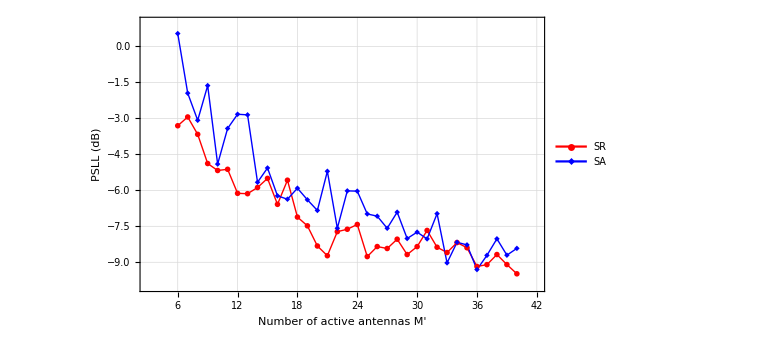

```mathematica
ListLinePlot[{Transpose[{xRange,psllListSR}],Transpose[{xRange,psllListSA}]},PlotMarkers->{{●,7},{◆,8}},(*Adds dots at the points*)PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},Frame->True,FrameStyle->{Black,None,Black,None},FrameLabel->{Style["Number of active antennas M'",FontFamily->"Times",FontSize->18,Black],Style["PSLL  (dB)",FontFamily->"Times",FontSize->16,Black]},FrameTicksStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"],PlotLegends->Placed[LineLegend[{"SR","SA"},LegendLayout->"Column",Background->White,FrameStyle->Black,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{0.8,0.8}],GridLines->{Automatic,Automatic},GridLinesStyle->Directive[Dashed,Gray],PlotRange->{{3,42},{1,-10}},AspectRatio->0.6,ImagePadding->{{60,10},{60,10}} (*Prevents clipping*),ImageSize->Large]
```

```mathematica
powerListRatioSR=excitationPatternList[[All,3]][[All,2]]/excitationPatternList[[All,3]][[All,1]];
powerListRatioSR=Map[Min,excitationPatternList[[All,3]]]/Map[Max,excitationPatternList[[All,3]]];
powerListRatioSA=Map[Min,excitationPatternListSA[[All,3]]]/Map[Max,excitationPatternListSA[[All,3]]];
```

```mathematica
ListLinePlot[{Transpose[{xRange,powerListRatioSR}],Transpose[{xRange,powerListRatioSA}]},PlotMarkers->{{●,7},{◆,8}},(*Adds dots at the points*)PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]},Frame->True,FrameStyle->{Black,None,Black,None},FrameLabel->{Style["Number of active antennas M'",FontFamily->"Times",FontSize->18,Black],Style[" MMPR ",FontFamily->"Times",FontSize->16,Black]},FrameTicksStyle->Directive[Black,FontSize->16,FontFamily->"Times New Roman"],PlotLegends->Placed[LineLegend[{"SR","SA"},LegendLayout->"Column",Background->White,LabelStyle->{FontFamily->"Times New Roman",FontSize->16}],{0.8,0.8}],GridLines->{Automatic,Automatic},GridLinesStyle->Directive[Dashed,Gray],PlotRange->{{3,42},{0.8,1.05}},AspectRatio->0.6,ImagePadding->{{60,10},{60,10}} (*Prevents clipping*),ImageSize->Large]
```

-Graphics-

```mathematica
Mean[powerListRatioSR]
```

0.931881

```mathematica
Mean[powerListRatioSA]
```

0.929523

#### Analyze the beam pattern behaviour for different active receiver count: Table 03

Considering  3 reciever positions(incluing the previosuly considered R_1 and R_2 and a new reciever R_3)

```mathematica
userLocations3={{1.6,2.3,0.75},{2.5,0.8,0.75},{2.3,1.6,0.75}};
```

```mathematica
clusterExcitationPattern3Users=clusterThinningAlgo[userLocations3,30,weightCombination1]
```

{{{1,1,1,0,0,1,0,0},{1,1,1,1,0,1,1,0},{1,1,0,1,1,1,0,0},{1,1,1,1,0,1,0,0},{1,1,1,1,1,0,1,0},{0,1,1,1,0,0,0,1}},19630.8,855.636,1464.85}

```mathematica
thinnedClusterRadiation3Users=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations3]*clusterExcitationPattern3Users[[1]],2]];
thinnedDatapair3UsersMax=Max[ParallelTable[thinnedClusterRadiation3Users,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

Finding PSLL for the obtained excitation pattern

```mathematica
thinnedPlotDataPair3Users=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiation3Users/thinnedDatapair3UsersMax]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
psllResult3Users=findPlanarSLL[userLocations3,thinnedDatapair3UsersMax,clusterExcitationPattern3Users[[1]]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[psllResult3Users[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult3Users[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -8.02 dB
PSLL Location : | {2.7,0.85,0.75}

Finding the MMPR for receivers

```mathematica
userPowerList3Users=beamPowerForUsers[thinnedClusterRadiation3Users,userLocations3,10*10^-3];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Min[userPowerList3Users]/Max[userPowerList3Users]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.88409

Consider 4 reciever positions(incluing the previosuly considered R_1 and R_2 , R_3 and a new reciever R_4)

```mathematica
userLocations4={{1.6,2.3,0.75},{2.5,0.8,0.75},{2.3,1.6,0.75},{1,1,0.75}};
```

```mathematica
clusterExcitationPattern4Users=clusterThinningAlgo[userLocations4,30,weightCombination1]
```

{{{0,1,1,1,1,1,0,1},{1,1,1,1,0,1,1,0},{1,0,0,1,1,1,0,0},{1,1,1,1,0,1,0,0},{0,1,1,1,0,1,0,0},{1,1,0,1,1,0,0,1}},10480.8,584.782,1215.89}

```mathematica
thinnedClusterRadiation4Users=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations4]*clusterExcitationPattern4Users[[1]],2]];
thinnedDatapair4UsersMax=Max[ParallelTable[thinnedClusterRadiation4Users,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair4Users=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiation4Users/thinnedDatapair4UsersMax]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
```

Finding PSLL for the obtained excitation pattern

```mathematica
psllResult4Users=findPlanarSLL[userLocations4,thinnedDatapair4UsersMax,clusterExcitationPattern4Users[[1]]];
Grid[{{Style["PSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[psllResult4Users[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["PSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult4Users[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

PSLL Value   : | -6.43 dB
PSLL Location : | {2.2,1.75,0.75}

Finding the MMPR for receivers

```mathematica
userPowerList4Users=beamPowerForUsers[thinnedClusterRadiation4Users,userLocations4,10*10^-3];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[userPowerList4Users]/Max[userPowerList4Users],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.814

Consider 5 reciever positions(incluing the previosuly considered R_1 and R_2 , R_3, R_4 and a new reciever R_5)

```mathematica
userLocations5={{1.6,2.3,0.75},{2.5,0.8,0.75},{2.3,1.6,0.75},{1,1,0.75},{1.5,3.5,0.75}};
```

```mathematica
clusterExcitationPattern5Users=clusterThinningAlgo[userLocations5,30,weightCombination1]
```

{{{1,0,1,0,1,1,0,1},{1,1,1,0,1,1,1,1},{1,1,1,1,1,1,0,1},{1,1,0,0,0,1,0,0},{0,1,0,1,0,0,1,0},{0,1,0,1,1,0,1,1}},4898.03,260.381,657.541}

```mathematica
thinnedClusterRadiation5Users=Abs[Total[beamFocusingPatternPlanar[λd,λe,x,y,0.75,Dis1,dis1,mx1,my1,nx1,ny1,xMiddle,yMiddle,userLocations5]*clusterExcitationPattern5Users[[1]],2]];
thinnedDatapair5UsersMax=Max[ParallelTable[thinnedClusterRadiation5Users,{x,0,xLength,0.1},{y,0,yLength,0.1}]];
```

```mathematica
thinnedPlotDataPair5Users=Flatten[ParallelTable[{y,x,20*Log[10,thinnedClusterRadiation5Users/thinnedDatapair5UsersMax]},{y,0,yLength,0.05},{x,0,xLength,0.05}],1];
```

Finding PSLL for the obtained excitation pattern

```mathematica
psllResult5Users=findPlanarSLL[userLocations5,thinnedDatapair5UsersMax,clusterExcitationPattern5Users[[1]]];
Grid[{{Style["LSLL Value   :",FontFamily->"Times New Roman",FontWeight->"Bold"],Row[{Round[psllResult5Users[[1]],0.01],Style[" dB",FontFamily->"Times New Roman"]}]},{Style["LSLL Location :",FontFamily->"Times New Roman",FontWeight->"Bold"],psllResult5Users[[2]]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

LSLL Value   : | -5.52 dB
LSLL Location : | {1.85,1.85,0.75}

Finding the MMPR for receivers

```mathematica
userPowerList5Users=beamPowerForUsers[thinnedClusterRadiation5Users,userLocations5,10*10^-3];
Grid[{{Style["Min max power ratio (MMPR) : ",FontFamily->"Times New Roman",FontWeight->"Bold"],Round[Min[userPowerList5Users]/Max[userPowerList5Users],0.001]}},Frame->All,Alignment->Center,BaseStyle->{FontSize->14,FontFamily->"Times New Roman"},ItemSize->{Automatic,2},Spacings->{2,2}]
```

Min max power ratio (MMPR) :  | 0.614